```mathematica
ClearAll["Global`*"];(*first part*)
r0 = 0.5;Bf[x_,y_,z_]:=(r={x,y,z};l1[θ_]:={r0 Cos[θ],r0 Sin[θ],r0/2};l2[θ_]:={r0 Cos[θ],r0 Sin[θ],-r0/2};
x1[θ_]:=r-{r0 Cos[θ],r0 Sin[θ],r0/2};r2[θ_]:=r-{r0 Cos[θ],r0 Sin[θ],-r0/2};dl1[θ_]:={r0 Sin[θ],-r0 Cos[θ],0}/Norm[{r0 Sin[θ],-r0 Cos[θ],0}];dl2[θ_]:={r0 Sin[θ],-r0 Cos[θ],0}/Norm[{r0 Sin[θ],-r0 Cos[θ],0}];
B=Sum[(Cross[dl1[θ],x1[θ]]/(Norm[x1[θ]])^3+Cross[dl2[θ],r2[θ]]/(Norm[r2[θ]])^3),{θ,0,2Pi,.001}]);(*we can use do loop instead*)
```

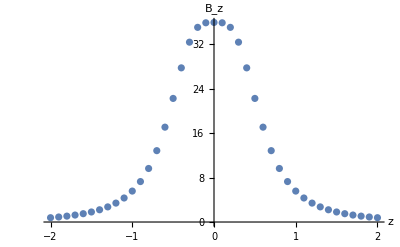

```mathematica
z0 = Range[-4 r0,4 r0,0.1];
Bcoil=Table[1/1000 Norm[Bf[0,0,z][[3]]],{z,-4 r0,4 r0,.1}];(*scaling B field*)
pp = Table[{z0[[i]],Bcoil[[i]]},{i,Length[z0]}];
ListPlot[pp,AxesLabel->{"z","B_z"},PlotRange->All]
```

-Graphics3D-

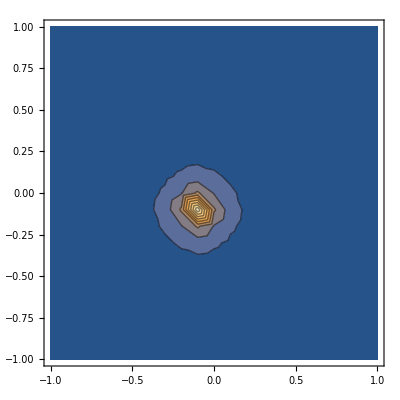

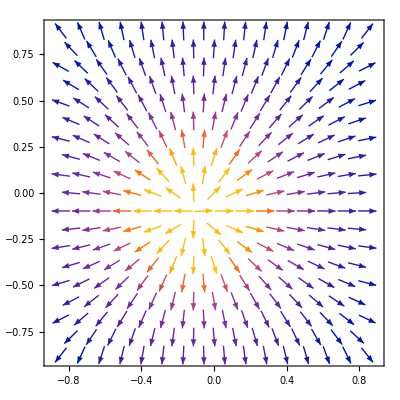

```mathematica
(*secend part 
continuing what was done in the lecture *)
dx=.1;q=1; 
x=Range[-1,1,dx];
y=Range[-1,1,dx];
z=Range[-1,1,dx];V1={};
V=Table[0,{i,Length[x]},{j,Length[y]},{k,Length[z]}];

ρ[x_,y_,z_]:=If[x==0&&y==0&&z==0,q/dx^3,0];
Vo= 0 V;
Vo[[;;,;;,;;]]=1;
While[Max[Abs[Vo-V]]>10^-6,Vo=V;Do[Do[Do[V[[i,j,k]]=1/6 (V[[i+1,j,k]]+V[[i-1,j,k]]+V[[i,j+1,k]]+V[[i,j-1,k]]+V[[i,j,k+1]]+V[[i,j,k-1]])+(ρ[-1+i dx,-1+j dx,-1+k dx] (dx)^2)/6;,{i,2,Length[x]-1}],{j,2,Length[y]-1}],{k,2,Length[z]-1}]]
Do[Do[V1=Append[V1,{x[[i]],x[[j]],V[[i,j,Round[Length[x]/2]]]}],{i,1,Length[x]}],{j,1,Length[x]}]
ListPlot3D[V1,PlotRange->All,Mesh->All]
ListContourPlot[V1,PlotRange->All]
Field=Table[{0,0},{i,Length[x]},{j,Length[y]}];
Do[Do[Field[[i,j]]=-1/(2dx){V[[i+1,j,Round[Length[x]/2]]]-V[[i-1,j,Round[Length[x]/2]]],V[[i,j+1,Round[Length[x]/2]]]-V[[i,j-1,Round[Length[x]/2]]]},{i,2,Length[x]-1}],{j,2,Length[y]-1}]
ListVectorPlot[Table[{{x[[i]],x[[j]]},Field[[i,j]]},{i,2,Length[x]-1},{j,2,Length[x]-1}]]
```

```mathematica
(* third part *)
```

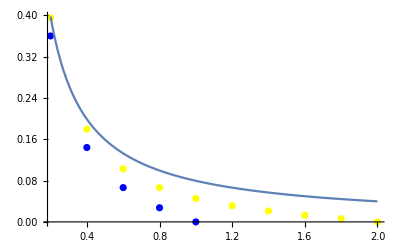

```mathematica
ClearAll["Global`*"];
dx=0.2;
x1=Range[-1,1,dx];
x2=Range[-2,2,dx];
y=Range[-1,1,.1];
z=Range[-1,1,.1];
V1=Table[0,{i,Length[x1]},{j,Length[y]},{k,Length[z]}];
V2=Table[0,{i,Length[x2]},{j,Length[y]},{k,Length[z]}];

ρ[x_,y_,z_]:=If[x==0&&y==0&&z==0,1/dx^3,0];
Pe[r_]=1/(4π r);
err=10^-6;
Vl10= 0 V1;
Vl20= 0 V2;
Vl10[[;;,;;,;;]]=1;
Vl20[[;;,;;,;;]]=1;
While[Max[Abs[Vl10-V1]]>err,Vl10=V1;Do[Do[Do[V1[[i,j,k]]=1/6 (V1[[i+1,j,k]]+V1[[i-1,j,k]]+V1[[i,j+1,k]]+V1[[i,j-1,k]]+V1[[i,j,k+1]]+V1[[i,j,k-1]])+1/6 ρ[-1+(i-1) dx,-1+(j-1) dx,-1+(k-1) dx] (dx)^2;,{i,2,Length[x1]-1}],{j,2,Length[x1]-1}],{k,2,Length[x1]-1}]]
While[Max[Abs[Vl20-V2]]>err,Vl20=V2;Do[Do[Do[V2[[i,j,k]]=1/6 (V2[[i+1,j,k]]+V2[[i-1,j,k]]+V2[[i,j+1,k]]+V2[[i,j-1,k]]+V2[[i,j,k+1]]+V2[[i,j,k-1]])+1/6 ρ[-2+(i-1)dx,-2+(j-1) dx,-2+(k-1) dx] (dx)^2;,{i,2,Length[x2]-1}],{j,2,Length[x2]-1}],{k,2,Length[x2]-1}]]
Vl1=Table[{(j) dx,V1[[(Length[x1]+1)/2+j,(Length[x1]+1)/2,(Length[x1]+1)/2]]},{j,1,(Length[x1]-1)/2}];
Vl2=Table[{(j) dx,V2[[(Length[x2]+1)/2+j,(Length[x2]+1)/2,(Length[x2]+1)/2]]},{j,1,(Length[x2]-1)/2}];
fig1=ListPlot[Vl1,PlotStyle->{Dot,Blue}];
fig2=ListPlot[Vl2,PlotStyle->{Dot,Yellow}];
fig3=Plot[Pe[r],{r,0.2,2},PlotRange->All];
Show[{fig1,fig2,fig3},PlotRange->All]
```